# Ph3 Set 5

## Jacob Snyder

## 5/8/19

```mathematica
data=Import["~/Downloads/getwfm.isf"]
data2=Most[data]
```

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024},{}}
 |  |  |  |

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024}}
 |  |  |  |

```mathematica
data2=Table[data[[i]],{i,Length[data]-1}]
```

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024}}
 |  |  |  |

```mathematica
nn=Length@data2;
w[n_]:=0.5*(1-Cos[2*Pi*(n-1)/nn]);
window=Table[w[n],{n,1,10000}];
```

```mathematica
newdata=Map[{data2[[#,1]],data2[[#,2]]*w[#]}&,Range[10000]]
```

{{-0.01,0.},{-0.009998,3.15827×10^-9},{-0.009996,1.42122×10^-8},{-0.009994,3.55306×10^-8},{-0.009992,8.84316×10^-8},9990,{0.00999,0.},{0.009992,0.},{0.009994,7.10611×10^-9},{0.009996,7.89568×10^-9},{0.009998,2.3687×10^-9}}
 |  |  |  |

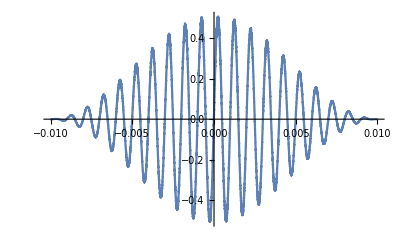

```mathematica
windplot=ListPlot[newdata,Joined->True]
```

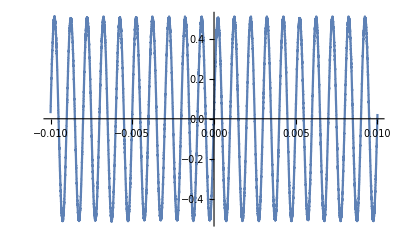

```mathematica
ListPlot[data2,Joined->True]
```

```mathematica
Export["~/Desktop/Hann.pdf",windplot,"PDF"]
```

~/Desktop/Hann.pdf

```mathematica
Export["~/Desktop/Hann.txt",newdata]
```

~/Desktop/Hann.txt